```mathematica
Quit[]
```

```mathematica
v=246;
vu=v s;
vd=v c;
mz=90;
mw=80;
al=-80;
ak=-800;
kl=10;
Plot3D[{Sqrt[Eigenvalues[{{mz^2 Cos[beta]^2+(al/1.414+x/2*kl) x Tan[beta],-mz^2 Sin[beta]Cos[beta]-al/1.414 x-kl x^2/2},{-mz^2 Sin[beta]Cos[beta]-al/1.414 x-kl x^2/2,mz^2 Sin[beta]^2+(al/1.414+x/2*kl) x/Tan[beta]}}]][[1]],Eigenvalues[{{mz^2 Cos[beta]^2+(al/1.414+x/2*kl) x Tan[beta],-mz^2 Sin[beta] Cos[beta]-al/1.414 x-kl x^2/2},{-mz^2 Sin[beta] Cos[beta]-al/1.414 x-kl x^2/2,mz^2 Sin[beta]^2+(al/1.414+x/2*kl) x/Tan[beta]}}][[2]],Sqrt[2*kl^2 x^2+kl x/1.414*ak],Sqrt[-3*ak*kl x],Sqrt[mw^2+1/Sin[2beta]*(2*al/1.414 x+kl x^2)]}/.{beta->ArcTan[t],x->y},{y,50,1600},{t,3,55},PlotStyle->{{Hue[0.5],Thick},{Purple,Thick},{Green,Thick},{Red,Thick},{Blue,Thick}}]
```

-Graphics3D-

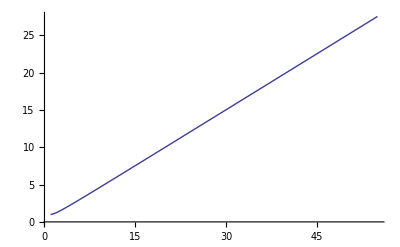

```mathematica
Plot3D[{kl,0.1,10},{ak,-800,0}]
```

```mathematica
v=246;
vu=v s;
vd=v c;
mz=90;
mw=80;
al=80;
ak=800;
kl=10;
{Sqrt[Eigenvalues[{{mz^2 Cos[beta]^2+(al/1.414+x/2*kl) x Tan[beta],-mz^2 Sin[beta] Cos[beta]-al/1.414 x-kl x^2/2},{-mz^2 Sin[beta] Cos[beta]-al/1.414 x-kl x^2/2,mz^2 Sin[beta]^2+(al/1.414+x/2*kl) x/Tan[beta]}}]][[1]],Sqrt[Eigenvalues[{{mz^2 Cos[beta]^2+(al/1.414+x/2*kl) x Tan[beta],-mz^2 Sin[beta] Cos[beta]-al/1.414 x-kl x^2/2},{-mz^2 Sin[beta] Cos[beta]-al/1.414 x-kl x^2/2,mz^2 Sin[beta]^2+(al/1.414+x/2*kl) x/Tan[beta]}}]][[2]],Sqrt[2*kl^2 x^2+kl x/1.414*ak],Sqrt[3*ak*kl x],Sqrt[mw^2+1/Sin[2beta]*(2*al/1.414 x+kl x^2)]}/.{x->(0.00141443 (-500. al+Sqrt[250000. al^2+499849. kl y^2 Sin[2. beta]]))/kl,beta->ArcTan[t]};
Plot3D[%,{y,50,500},{t,3,55},PlotStyle->{{Hue[0.5],Thick},{Purple,Thick},{Green,Thick},{Red,Thick},{Blue,Thick}},AxesOrigin->{50,0}]
```

Plot3D::exclul: {Re[t] - 0, 4.99849×10^6\ Im[y^2\ Sin[2.\ beta]] - 0, « 12 », Im[((-0.00800243 + 0.\ ⅈ)\ Plus[« 2 »] - 1.00031×10^-7\ Power[« 2 »] - (4050.  + 0.\ ⅈ)\ Sin[« 1 »])^2 - (0.000282886  + 0.\ ⅈ)\ (-40000. + √Plus[« 2 »])\ ((229137.  + 0.\ ⅈ) - (2.91038×10^-11 + 0.\ ⅈ)\ Cos[« 1 »] + (229137.  + 0.\ ⅈ)\ Cos[« 1 »] + 2.86422\ Plus[« 2 »] + 2.86422\ Cos[« 1 »]\ Plus[« 2 »])\ Sin[2\ ArcTan[« 1 »]]] - 0, Im[(1.  + 0.\ ⅈ)\ Csc[2\ ArcTan[t]]\ ((0.00800243  + 0.\ ⅈ)\ (-40000. + Power[« 2 »]) + 1.00031×10^-7\ Plus[« 2 »]^2 + (4050.  + 0.\ ⅈ)\ Sin[Times[« 2 »]] - √Plus[« 2 »])] - 0}
 must be a list of equalities or real-valued functions.

Plot3D::exclul: {Re[t] - 0, 4.99849×10^6\ Im[y^2\ Sin[2.\ beta]] - 0, « 13 », Im[(1.  + 0.\ ⅈ)\ Csc[2\ ArcTan[t]]\ ((0.00800243  + 0.\ ⅈ)\ (-40000. + Power[« 2 »]) + 1.00031×10^-7\ Plus[« 2 »]^2 + (4050.  + 0.\ ⅈ)\ Sin[Times[« 2 »]] + √Power[« 2 »] + Times[« 4 »])] - 0}
 must be a list of equalities or real-valued functions.

Plot3D::exclul: {4.99849×10^6\ Im[y^2\ Sin[2.\ beta]] - 0, 4.99849×10^6\ Im[y^2\ Sin[2.\ beta]] - 0, (0.800243\ Im[√1.6×10^9 + Times[« 3 »]] + 4.00122×10^-6\ Im[(-40000. + Power[« 2 »])^2]) - 0} must be a list of equalities or real-valued functions.

General::stop: Further output of Plot3D :: exclul will be suppressed during this calculation.

$Aborted

```mathematica
{Sqrt[Eigenvalues[{{mz^2 Cos[beta]^2+(al/1.414+x/2*kl) x Tan[beta],-mz^2 Sin[beta] Cos[beta]-al/1.414 x-kl x^2/2},{-mz^2 Sin[beta] Cos[beta]-al/1.414 x-kl x^2/2,mz^2 Sin[beta]^2+(al/1.414+x/2*kl) x/Tan[beta]}}]][[1]],Sqrt[Eigenvalues[{{mz^2 Cos[beta]^2+(al/1.414+x/2*kl) x Tan[beta],-mz^2 Sin[beta] Cos[beta]-al/1.414 x-kl x^2/2},{-mz^2 Sin[beta] Cos[beta]-al/1.414 x-kl x^2/2,mz^2 Sin[beta]^2+(al/1.414+x/2*kl) x/Tan[beta]}}]][[2]],Sqrt[2*kl^2 x^2+kl x/1.414*ak],Sqrt[3*ak*kl x],Sqrt[mw^2+1/Sin[2beta]*(2*al/1.414 x+kl x^2)]}/.{x->(0.00141443 (-500. al+Sqrt[250000. al^2+499849. kl y^2 Sin[2. beta]]))/kl,beta->ArcTan[t]}//Simplify
```

{√(Csc[2 ArcTan[t]] ((0.000643396+0. ⅈ)+0.500002 y^2 Sin[2. beta]-(1.60849×10^-8+0. ⅈ) √(1.6×10^9+4.99849×10^6 y^2 Sin[2. beta])+(4050.+0. ⅈ) Sin[2 ArcTan[t]]-1. √((-0.000282886+0. ⅈ) (-40000.+√(1.6×10^9+4.99849×10^6 y^2 Sin[2. beta])) ((114568.+0. ⅈ)-(2.91038×10^-11+0. ⅈ) Cos[2 ArcTan[t]]+2.86422 √(1.6×10^9+4.99849×10^6 y^2 Sin[2. beta])+Cos[4 ArcTan[t]] ((114568.+0. ⅈ)+2.86422 √(1.6×10^9+4.99849×10^6 y^2 Sin[2. beta]))) Sin[2 ArcTan[t]]+((0.000643396+0. ⅈ)+0.500002 y^2 Sin[2. beta]-(1.60849×10^-8+0. ⅈ) √(1.6×10^9+4.99849×10^6 y^2 Sin[2. beta])+(4050.+0. ⅈ) Sin[2 ArcTan[t]])^2))),√(Csc[2 ArcTan[t]] ((0.000643396+0. ⅈ)+0.500002 y^2 Sin[2. beta]-(1.60849×10^-8+0. ⅈ) √(1.6×10^9+4.99849×10^6 y^2 Sin[2. beta])+(4050.+0. ⅈ) Sin[2 ArcTan[t]]+√((-0.000282886+0. ⅈ) (-40000.+√(1.6×10^9+4.99849×10^6 y^2 Sin[2. beta])) ((114568.+0. ⅈ)-(2.91038×10^-11+0. ⅈ) Cos[2 ArcTan[t]]+2.86422 √(1.6×10^9+4.99849×10^6 y^2 Sin[2. beta])+Cos[4 ArcTan[t]] ((114568.+0. ⅈ)+2.86422 √(1.6×10^9+4.99849×10^6 y^2 Sin[2. beta]))) Sin[2 ArcTan[t]]+((0.000643396+0. ⅈ)+0.500002 y^2 Sin[2. beta]-(1.60849×10^-8+0. ⅈ) √(1.6×10^9+4.99849×10^6 y^2 Sin[2. beta])+(4050.+0. ⅈ) Sin[2 ArcTan[t]])^2))),√(-19205.8+20.0001 y^2 Sin[2. beta]+0.480145 √(1.6×10^9+4.99849×10^6 y^2 Sin[2. beta])),1.84245 √(-40000.+√(1.6×10^9+4.99849×10^6 y^2 Sin[2. beta])),√(6400+Csc[2 ArcTan[t]] (0.00128679+1. y^2 Sin[2. beta]-3.21698×10^-8 √(1.6×10^9+4.99849×10^6 y^2 Sin[2. beta])))}

```mathematica
Plot3D[%,{y,50,500},PlotStyle->{{Hue[0.5],Thick},{Purple,Thick},{Green,Thick},{Red,Thick},{Blue,Thick}},AxesOrigin->{50,0},Frame->True]
```

Plot3D::optx: Unknown option Frame in Plot3D[%, {y, 50, 500}, PlotStyle → {{Hue[0.5], Thick}, {Purple, Thick}, {Green, Thick}, {Red, Thick}, {Blue, Thick}}, AxesOrigin → {50, 0}, Frame → True].

Plot3D[%,{y,50,500},PlotStyle→{{Hue[0.5],Thick},{Purple,Thick},{Green,Thick},{Red,Thick},{Blue,Thick}},AxesOrigin→{50,0},Frame→True]

```mathematica
Solve[(al/1.414+x/2*kl) x 2/s2b==y^2,x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→0.000141443 (-40000.-3.16228 √(1.6×10^8+123040. y^2))},{x→0.000141443 (-40000.+3.16228 √(1.6×10^8+123040. y^2))}}

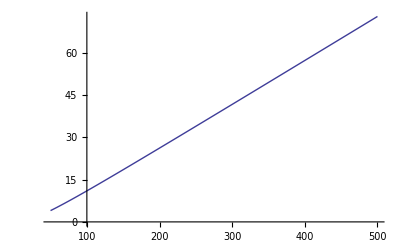

```mathematica
Plot[0.000141443 (-40000.+3.16228 Sqrt[1.6*10^8+123040. y^2]),{y,50,500}]
```

```mathematica
Plot[%,{y,50,800},PlotStyle->{{Hue[0.5],Thick},{Purple,Thick},{Green,Thick},{Red,Thick},{Blue,Thick}},PlotRange->{{50,800},{0,600}},AxesOrigin->{50,0},Frame->True,FrameLabel->{"m_A(GeV)", "m(GeV)"}]
```

-Graphics-

```mathematica
{Sqrt[2*0.15^2 x^2+0.15 x/1.414*80],Sqrt[Eigenvalues[{{mz^2 c^2+(80/1.414+x/2*0.15) x t,-mz^2 s c-80/1.414 x-0.15 x^2/2},{-mz^2 s c-80/1.414 x-0.15 x^2/2,mz^2 s^2+(80/1.414+x/2*0.15) x/t}}]][[1]]}/.x->0.000942951 (-400000.+3.16228 Sqrt[1.6*10^10+1.49955*10^6 y^2 s2b^2]);
```

```mathematica
aa=%18[[1]];
bb=%18[[2]];
```

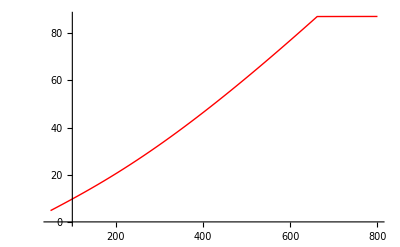

```mathematica
Plot[If[aa≤bb,aa,bb],{y,50,800},PlotStyle->{Red,Thick}]
```

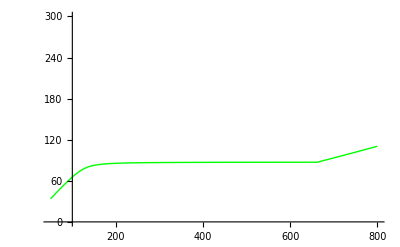

```mathematica
Plot[If[aa≤bb,bb,aa],{y,50,800},PlotStyle->{Green,Thick},PlotRange->{{50,800},{0,300}}]
```

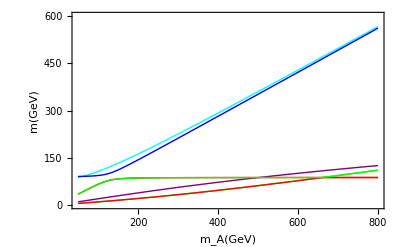

```mathematica
Show[%35,%25,%30]
```

```mathematica
beta=ArcTan[8];
t=Tan[beta];
s=Sin[beta];
c=Cos[beta];
s2b = Sin[2beta];
v=246;
vu=v s;
vd= v c;
mz=90;
mw=80;
```

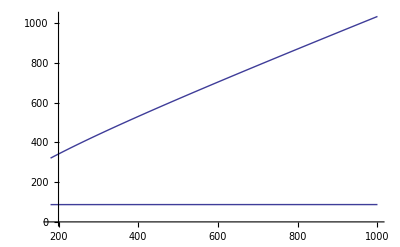

```mathematica
Plot[Sqrt[Eigenvalues[{{mz^2c^2+(80/1.414+x/2*0.15)x t,  -mz^2 s c -80/1.414 x-0.15 x^2/2},{-mz^2 s c-80/1.414 x-0.15 x^2/2,mz^2 s^2+(80/1.414+x/2*0.15) x /t}}]],{x,180,1000}]
```

```mathematica
Eigenvalues[{{mz^2 Cos[beta]^2+x^2 Tan[beta],-mz^2 Sin[beta] Cos[beta]-x^2},{-mz^2 Sin[beta] Cos[beta]-x^2,mz^2 Sin[beta]^2+x^2/Tan[beta]}}]//FullSimplify//TrigReduce
```

{1/8 (4 x^2 Csc[beta] Sec[beta]+2 mz^2 Csc[beta] Sec[beta] Sin[2 beta]-√2 Csc[beta] Sec[beta] √(mz^4+8 x^4-mz^4 Cos[4 beta]-8 mz^2 x^2 Cos[4 beta] Sin[2 beta])),1/8 (4 x^2 Csc[beta] Sec[beta]+2 mz^2 Csc[beta] Sec[beta] Sin[2 beta]+√2 Csc[beta] Sec[beta] √(mz^4+8 x^4-mz^4 Cos[4 beta]-8 mz^2 x^2 Cos[4 beta] Sin[2 beta]))}

```mathematica
Plot3D[{Sqrt[1/4 (2 mz^2+Csc[2 beta] (4 x^2-Sqrt[2] Sqrt[mz^4+8 x^4-mz^4 Cos[4 beta]+4 mz^2 x^2 Sin[2 beta]-4 mz^2 x^2 Sin[6 beta]]))],Sqrt[1/4 (2 mz^2+Csc[2 beta] (4 x^2+Sqrt[2] Sqrt[mz^4+8 x^4-mz^4 Cos[4 beta]+4 mz^2 x^2 Sin[2 beta]-4 mz^2 x^2 Sin[6 beta]]))],Sqrt[mw^2+x^2]}/.{beta->ArcTan[t],mz->90},{x,60,200},{t,3,55}]
```

-Graphics3D-

```mathematica
Plot3D[1/4 (2 mz^2+Csc[2 beta] (4 x^2+Sqrt[2] Sqrt[mz^4+8 x^4-mz^4 Cos[4 beta]+4 mz^2 x^2 Sin[2 beta]-4 mz^2 x^2 Sin[6 beta]]))/.mz->90,{x,50,500},{beta,ArcTan[3],ArcTan[55]}]
```

-Graphics3D-

```mathematica
Plot3D[{a+b,a-b},{a,1,2},{b,1,2}]
```

-Graphics3D-